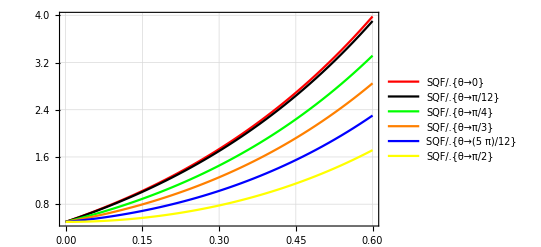

```mathematica
ClearAll["Global`*",Derivative,Subscript]
SQF=Subscript[w, 2]-1/2(*Squeezing parameter Subscript[S, θ] = <Subscript[X, θ]^2>-<Subscript[X, θ]>^2-1/2 *);
Subscript[w, 2]=1/2 (Subscript[q, 2] ⅇ^(-2ⅈ θ)+Subscript[q, 22] ⅇ^(2ⅈ θ)+2 Subscript[q, 3]);(*where Subscript[X, 2] = <Subscript[X, θ]^2> =1/2(2Re[<a^2>ⅇ^(-2ⅈ θ)]+2<a^+a>+1)=1/2(2Re[Subscript[Q, 2]*ⅇ^(-2ⅈ θ)]+2 Subscript[Q, 3]+1) *)
Subscript[q, 2]=1/Sinh[r]^2( 3  ⅇ^(ⅈ θ) Sinh[r]^3 Cosh[r] );
Subscript[q, 22]=1/Sinh[r]^2( 3  ⅇ^(-ⅈ θ) Sinh[r]^3 Cosh[r] );
Subscript[q, 3]=1/Sinh[r]^2(Sinh[r]^2 Cosh[r]^2+2 Sinh[r]^4)(* Subscript[f, 1]=<ξ , s/2 | a^+a^+aa|s/2,ξ > *);
Show[Plot[SQF/.{θ->0 },{r,0,0.6},PlotStyle->Red,PlotTheme->"Detailed",PlotRange->All],
Plot[SQF/.{θ->π/12 },{r,0,0.6},PlotStyle->Black,PlotTheme->"Detailed",PlotRange->All],Plot[SQF/.{θ->π/4 },{r,0,0.6},PlotStyle->Green,PlotTheme->"Detailed",PlotRange->All],Plot[SQF/.{θ->π/3},{r,0,0.6},PlotStyle->Orange,PlotTheme->"Detailed",PlotRange->All] ,Plot[SQF/.{θ->(5π)/12},{r,0,0.6},PlotStyle->Blue,PlotTheme->"Detailed",PlotRange->All] ,Plot[SQF/.{θ->π/2},{r,0,0.6},PlotStyle->Yellow,PlotTheme->"Detailed",PlotRange->All]  ]
```